```mathematica
附录C
```

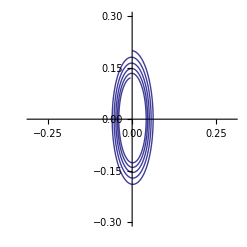

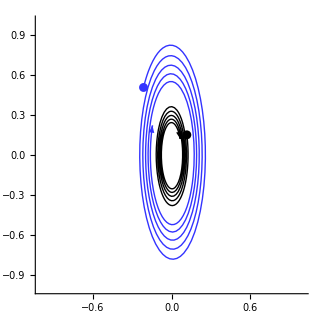
{EquationTrekkerState["θ''θt010","{}",TrekData["0.θ'", <>]
TrekData["0.θ'", <>], <>],-Graphics-}

```mathematica
<<EquationTrekker`
g=9.8;L=1.0;Ω=√(g/L);η=0.1;
v0=0.2;ω0=v0/L;tm=10;
s=NDSolve[{θ''[t]==-Ω^2 Sin[θ[t]]-η θ'[t],
θ[0]==0,θ'[0]==ω0},θ,{t,0,tm}];
ParametricPlot[{θ[t],θ'[t]}/.s[[1]],{t,0,tm},
AspectRatio->Automatic,
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003],
PlotRange->{{-0.3,0.3},{-0.3,0.3}}]
EquationTrekker[θ''[t]==-Ω^2 Sin[θ[t]]-η θ'[t],
θ,{t,0,tm},PlotStyle->Thickness[0.004]]
Clear[g,L,Ω,η,v0,ω0,θ,tm,s,α]
```

```mathematica
EquationTrekker[First[s]]
```

```mathematica
EquationTrekker[θ''[t]==-Ω^2 Sin[θ[t]]-η θ'[t],
θ,{t,0,tm}]
```

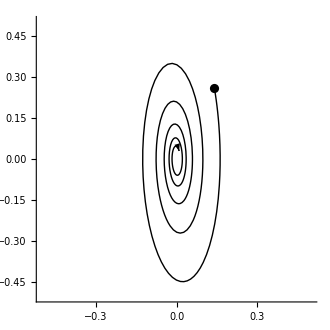
{EquationTrekkerState["θ''θt010","{L → 1., η → 0.5}",TrekData["0.θ'", <>], <>],-Graphics-}

```mathematica
<< EquationTrekker`
g=9.8;tm=10;Ω=√(g/L);
EquationTrekker[θ''[t]==-Ω^2 Sin[θ[t]]-η θ'[t],
θ,{t,0,tm},
TrekParameters->{η->0.5,L->1},
PlotRange->{{-0.5,0.5},{-0.5,0.5}},PlotStyle->Thickness[0.004]]
Clear[g,L,Ω,η,θ]
```